# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.90859197873988×10^9

#### 変数

```mathematica
date="20231001"
```

20231001

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231001.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231001.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

20179344 184584284 8129775211 log-20231001.rcoslog0003.log

ckan

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231001/T=ci.P~5

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

10350645

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{10350645,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90511×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-09-30T15:00:00Z
log.ci0001.aws.wa01.yobi
160.16.209.208
host":"-
user":"-
3.90511×10^9
method":"GET
https://cir.nii.ac.jp/crid/1572824498935466624.json
code":"200
size":"1069
-
agent":"Ruby
http_x_forwarded_for":"\"160.16.209.208\"
request_time":"0.010
upstream_response_time":"0.010"}

```mathematica
(*strSplt1CCCC["ci"]=strSplt1CCCCpre["ci"]*)
```

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "css".

StringTake::take: Cannot take positions 1 through 19 in "Graphics".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-09-30T15:00:00Z
log.ci0001.aws.wa01.yobi
160.16.209.208
host":"-
user":"-
3.90511×10^9
method":"GET
https://cir.nii.ac.jp/crid/1573668925025143936.json
code":"200
size":"690
-
agent":"Ruby
http_x_forwarded_for":"\"160.16.209.208\"
request_time":"0.008
upstream_response_time":"0.008"}
1573668925025143936
toCRID[-]

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231001/T=cs.R=.P=

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

4920

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{4920,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{4920,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/v2/gh/jxta/yamryo_notebooks/master?filepath=Research%2FWord_and_FreeGroup.ipynb

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-10-01T00:07:18.839628519+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-09-30T15:28:14Z
log.cs0002.ksw.wa01.yobi
35.213.23.14
stream":"stdout
user":"-
3.90511×10^9
date_time":"30/Sep/2023:15:28:14 +0000
https://jupyter.cs.rcos.nii.ac.jp/hub/login?next=%2Fhub%2Fhome
method":"GET
code":"302
https://openidp.nii.ac.jp/idp/profile/SAML2/Redirect/SSO?execution=e1s3
agent":"Mozilla/5.0 (X11; Linux x86_64) AppleWebKit/537.36 (KHTML, like Gecko) HeadlessChrome/88.0.4324.150 Safari/537.36
size":"0
hostname":"fluentd-bllnp"}

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231001/T=la.T~ea.A~hc.A~go.A~bot.P~api

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

8458

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{8458,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0001.aws.wa01.yobi,8456},{log.la0002.aws.wa01.yobi,1},{log.la0003.aws.wa01.yobi,1}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{8456,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{1,12}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{1,12}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-30T15:04:29Z
log.la0001.aws.wa01.yobi
{"user":"-
date_time":"01/Oct/2023:00:04:29 +0900
method":"GET
path":"/mod/url/view.php?id=1544&forceview=1
code":"200
size":"14071
referer":"-
agent":"Mozilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.5938.92 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)
http_x_forwarded_for":"66.249.79.192
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{8456,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-30T23:46:23Z
log.la0002.aws.wa01.yobi
{"user":"-
date_time":"30/Sep/2023:23:46:23 +0000
method":"GET
path":"/
code":"302
size":"242
referer":"-
agent":"fasthttp
http_x_forwarded_for":"146.190.113.237
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{1,12}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-30T23:49:01Z
log.la0003.aws.wa01.yobi
{"user":"-
date_time":"30/Sep/2023:23:49:01 +0000
method":"GET
path":"/
code":"302
size":"-
referer":"-
agent":"fasthttp
http_x_forwarded_for":"146.190.113.237
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{1,12}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{8458,12}

```mathematica
strSplt1R["la"][[1]]
```

{2023-09-30T15:04:29Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"66.249.79.192,size":"14071,method":"GET,date_time":"01/Oct/2023:00:04:29 +0900,code":"200,path":"/mod/url/view.php?id=1544&forceview=1,{"user":"-,session_id":"-"},referer":"-,agent":"Mozilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.5938.92 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.90511×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2023-09-30T15:04:29Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"66.249.79.192
size":"14071
method":"GET
3.90514×10^9
code":"200
https://lms.nii.ac.jp/mod/url/view.php?id=1544&forceview=1
{"user":"-
session_id":"-"}
-
agent":"Mozilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.5938.92 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{8458,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2023-09-30T15:04:29Z
log.la0001.aws.wa01.yobi
66.249.79.192
size":"14071
method":"GET
3.90514×10^9
code":"200
https://lms.nii.ac.jp/mod/url/view.php?id=1544&forceview=1
{"user":"-
session_id":"-"}
-
agent":"Mozilla/5.0 (Linux; Android 6.0.1; Nexus 5X Build/MMB29P) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.5938.92 Mobile Safari/537.36 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231001/T=wk.P~4.A~bot

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

1358

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{1358,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{1358,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-09-30T15:07:04+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.90511×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-09-30T16:39:28Z
log.wk1001.oci.wa01.yobi
188.165.215.206
user":"-
method":"GET
3.90511×10^9
code":"200
https://jdcat.jsps.go.jp/
size":"11280
http_x_forwarded_for":"188.165.215.206, 162.158.86.246, 46.101.158.159"}
-
agent":"Mozilla/5.0 (compatible; MJ12bot/v1.4.8; http://mj12bot.com/)

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
Timing[(strSplt1CCCC[3]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{97.9055,{10356923}}

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{92.6648,{10365381}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{10365381}

### ckanデータの処理(基盤統合)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{10365381}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

115

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

115

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{10365381}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

6

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

6

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

119

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

119

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{93.4884,{10350645,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-10-01T11:34:38Z
log.ci0001.aws.wa01.yobi
100.0.27.192
host":"-
user":"-
3.90518×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130282270618973056
code":"200
size":"12323
https://scholar.google.com/
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.0.0 Safari/537.36
http_x_forwarded_for":"\"100.0.27.192\"
request_time":"0.066
upstream_response_time":"0.066"}
1130282270618973056
toCRID[https://scholar.google.com/]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{10350645}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690294973956683136,1690857923909290240,1690576448930598656,1690857923899904512,1690294973945633024,1690857923907121152,1690013498976992640,1690294973953385728,1690576448933966976,1690576448933966976,1690576448923813248,1690294973952864000,1690857923906848512,1690857923906848512,1690857923901881472,1690294973947311744,1690013498976715264,1690294973945633024,1690294973945633024,1690576448929039488,1690013498976558080,1690294973952864000,1690013498969469312,1690013498969469312,1690013498968713216,1690576448929428480,1690294973953142784,1690857923900396032,1690013498966095744,1690576448933580288,1690576448933580288,1690857923906664192,1690576448927221376,1690576448927621632,1690294973946036352,1690013552764995456,1690857923901283200,1690857923907952128,1690294973952864000,1690294973948571008,1690013498968050432,1690857923907960832,1690294973943660544,1690294973943660544,1690294973941437184,1690576448920900992,1690576448934078720,1690576448928548480,1690294973954258560,1690294973952823040,1690013498968050432,1690857923908044032,1690013498978176640,1690295027741403904,1690295027741492224,1690576448929342208,1690013498970167808,1690857923904243328,1690013498964705792,1690576448927702912,1690576448928309376,1690294973941671168,1690857923897584512,1690013498977721216,1690857923905442176,1690576502718069120,1690576448926369664,1690576448923416704,1690576448924068224,1690576448931094784,1690857923910933376,1690013552764649856,1690857923911438848,1690857923910663680,1690294973948300288,1690857923900836864,1690576448931792768,1690013498973596416,1690576502718167424,1690576448932968576,1690013498965989504,1690013498977721472,1690013498965485568,1690013498965703424,1690294973946921728,1690576502718063360,1690013498971913728,1690857923911553920,1690857923897065472,1690576502718070912,1690013498969802752,1690576448932109184,1690013498976681728,1690294973955526144,1690013498978093952,1690013498977224704,1690013552764650240,1690294973947157760,1690576448933285888,1690013498974165248,1690013498977837696,1690576448920858240,1690013498967909120,1690576502718063872,1690576448932783360,1690294973954617728,1690857923907371392,1690294973957105536,1690857923899811072,1690576448934169472,1690294973943017856,1690576448925471104,1690576448920588416,1690295027741352832,1690857923911066880}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690294973945633024,1690294973945633024,1690857923907121152,1690857923906848512,1690857923906848512,1690576448933580288}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964705792,1690013498965485568,1690013498965703424,1690013498965989504,1690013498966095744,1690013498967909120,1690013498968050432,1690013498968713216,1690013498969469312,1690013498969802752,1690013498970167808,1690013498971913728,1690013498973596416,1690013498974165248,1690013498976558080,1690013498976681728,1690013498976715264,1690013498976992640,1690013498977224704,1690013498977721216,1690013498977721472,1690013498977837696,1690013498978093952,1690013498978176640,1690013552764649856,1690013552764650240,1690013552764995456,1690294973941437184,1690294973941671168,1690294973943017856,1690294973943660544,1690294973945633024,1690294973946036352,1690294973946921728,1690294973947157760,1690294973947311744,1690294973948300288,1690294973948571008,1690294973952823040,1690294973952864000,1690294973953142784,1690294973953385728,1690294973954258560,1690294973954617728,1690294973955526144,1690294973956683136,1690294973957105536,1690295027741352832,1690295027741403904,1690295027741492224,1690576448920588416,1690576448920858240,1690576448920900992,1690576448923416704,1690576448923813248,1690576448924068224,1690576448925471104,1690576448926369664,1690576448927221376,1690576448927621632,1690576448927702912,1690576448928309376,1690576448928548480,1690576448929039488,1690576448929342208,1690576448929428480,1690576448930598656,1690576448931094784,1690576448931792768,1690576448932109184,1690576448932783360,1690576448932968576,1690576448933285888,1690576448933580288,1690576448933966976,1690576448934078720,1690576448934169472,1690576502718063360,1690576502718063872,1690576502718069120,1690576502718070912,1690576502718167424,1690857923897065472,1690857923897584512,1690857923899811072,1690857923899904512,1690857923900396032,1690857923900836864,1690857923901283200,1690857923901881472,1690857923904243328,1690857923905442176,1690857923906664192,1690857923906848512,1690857923907121152,1690857923907371392,1690857923907952128,1690857923907960832,1690857923908044032,1690857923909290240,1690857923910663680,1690857923910933376,1690857923911066880,1690857923911438848,1690857923911553920}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964705792→True,1690013498965485568→True,1690013498965703424→True,1690013498965989504→True,1690013498966095744→True,1690013498967909120→True,1690013498968050432→True,1690013498968713216→True,1690013498969469312→True,1690013498969802752→True,1690013498970167808→True,1690013498971913728→True,1690013498973596416→True,1690013498974165248→True,1690013498976558080→True,1690013498976681728→True,1690013498976715264→True,1690013498976992640→True,1690013498977224704→True,1690013498977721216→True,1690013498977721472→True,1690013498977837696→True,1690013498978093952→True,1690013498978176640→True,1690013552764649856→True,1690013552764650240→True,1690013552764995456→True,1690294973941437184→True,1690294973941671168→True,1690294973943017856→True,1690294973943660544→True,1690294973945633024→True,1690294973946036352→True,1690294973946921728→True,1690294973947157760→True,1690294973947311744→True,1690294973948300288→True,1690294973948571008→True,1690294973952823040→True,1690294973952864000→True,1690294973953142784→True,1690294973953385728→True,1690294973954258560→True,1690294973954617728→True,1690294973955526144→True,1690294973956683136→True,1690294973957105536→True,1690295027741352832→True,1690295027741403904→True,1690295027741492224→True,1690576448920588416→True,1690576448920858240→True,1690576448920900992→True,1690576448923416704→True,1690576448923813248→True,1690576448924068224→True,1690576448925471104→True,1690576448926369664→True,1690576448927221376→True,1690576448927621632→True,1690576448927702912→True,1690576448928309376→True,1690576448928548480→True,1690576448929039488→True,1690576448929342208→True,1690576448929428480→True,1690576448930598656→True,1690576448931094784→True,1690576448931792768→True,1690576448932109184→True,1690576448932783360→True,1690576448932968576→True,1690576448933285888→True,1690576448933580288→True,1690576448933966976→True,1690576448934078720→True,1690576448934169472→True,1690576502718063360→True,1690576502718063872→True,1690576502718069120→True,1690576502718070912→True,1690576502718167424→True,1690857923897065472→True,1690857923897584512→True,1690857923899811072→True,1690857923899904512→True,1690857923900396032→True,1690857923900836864→True,1690857923901283200→True,1690857923901881472→True,1690857923904243328→True,1690857923905442176→True,1690857923906664192→True,1690857923906848512→True,1690857923907121152→True,1690857923907371392→True,1690857923907952128→True,1690857923907960832→True,1690857923908044032→True,1690857923909290240→True,1690857923910663680→True,1690857923910933376→True,1690857923911066880→True,1690857923911438848→True,1690857923911553920→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

101890

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{19.4442,{101890,1}}

```mathematica
idxLogS[4][[1]]
```

{{2023-10-01T11:34:38Z,log.ci0001.aws.wa01.yobi,100.0.27.192,host":"-,user":"-,3.90518×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130282270618973056,code":"200,size":"12323,https://scholar.google.com/,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.0.0 Safari/537.36,http_x_forwarded_for":"\"100.0.27.192\",request_time":"0.066,upstream_response_time":"0.066"},1130282270618973056,toCRID[https://scholar.google.com/],1},{2023-10-01T11:50:57Z,log.ci0001.aws.wa03.yobi,100.0.27.192,host":"-,user":"-,3.90518×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130282270618973056,code":"200,size":"12323,https://scholar.google.com/,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/117.0.0.0 Safari/537.36,http_x_forwarded_for":"\"100.0.27.192\",request_time":"0.080,upstream_response_time":"0.080"},1130282270618973056,toCRID[https://scholar.google.com/],2}}

```mathematica
idxLogSinf[4][[2]]
```

{{{2023-10-01T04:13:25Z,log.ci0001.aws.wa02.yobi,100.1.129.20,host":"-,user":"-,3.90515×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130282269412453248,code":"200,size":"12775,https://scholar.google.com/,agent":"Mozilla/5.0 (X11; CrOS x86_64 14541.0.0) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.0.0 Safari/537.36,http_x_forwarded_for":"\"100.1.129.20\",request_time":"0.067,upstream_response_time":"0.067"},1130282269412453248,toCRID[https://scholar.google.com/],3}}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/elecom/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story.

$Failed

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.00907,Null}

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://scholar.google.com/https://cir.nii.ac.jp/crid/1130282269412453248{3.90515×10^9,3}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

101890

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}];
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions]
```

{151.078,{101890,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ]
```

{216.235,{101890,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{101890,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

{https://scholar.google.com/https://cir.nii.ac.jp/crid/1130282270618973056{3.90518×10^9,1},https://scholar.google.com/https://cir.nii.ac.jp/crid/1130282270618973056{3.90518×10^9,2}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{152612,3}

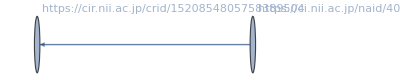
{20231001,{15,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{152612,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

{152612,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{134380,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{120993,3}

上が分離されたストーリー

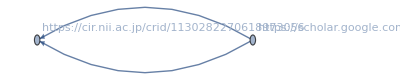
{20231001,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3[4][[1]]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
Directory[]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
(*Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]*)
```

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{120993}

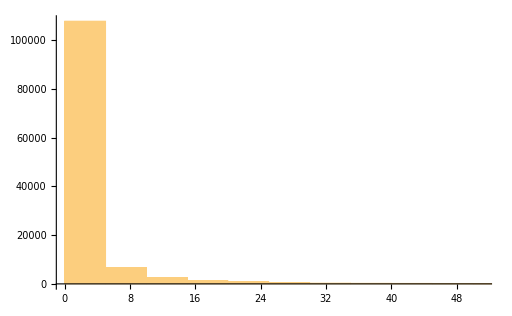

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{120993}

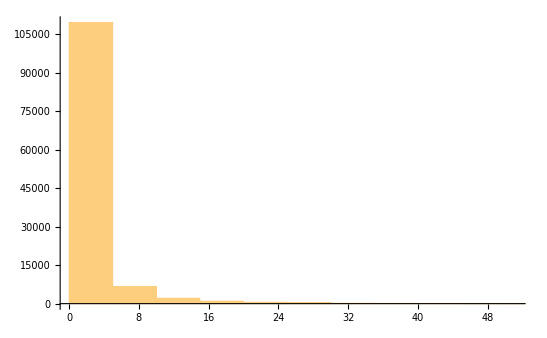

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{120993}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{120993}

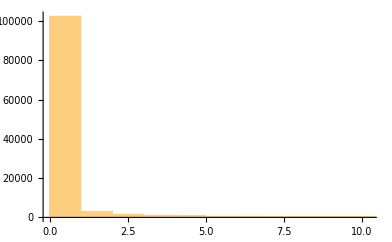

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{120993}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{120993}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{120993}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {porntrex.com} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{porntrex.com}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{120993}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{ci.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{20,26,27,123,155,156,159,167,246,262,304,309,332,409,451,482,544,545,566,568,751,1013}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,https:auth.cir.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:contents.nii.ac.jp,https:hosei.repo.nii.ac.jp,https:idp.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:kurume.repo.nii.ac.jp,https:lms.nii.ac.jp,https:minobu.repo.nii.ac.jp,https:nrid.nii.ac.jp,https:openidp.nii.ac.jp,https:ophub.rcos.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:support.nii.ac.jp,https:www.nii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*\\.nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*\\.jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{porntrex.com}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{porntrex.com}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{120993}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,111952},{1,9040},{3,1}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1172,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,76326},{2,44632},{0,35}}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{25,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 76221
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 24424
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 19680
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 119
https:cir.nii.ac.jp
https:support.nii.ac.jp | 68
 | 35
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 43
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 7
https:lms.nii.ac.jp | 95
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 195
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 69
https:cir.nii.ac.jp
https:minobu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:www.nii.ac.jp | 4
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 3
https:jupyter.cs.rcos.nii.ac.jp | 9
https:cir.nii.ac.jp
https:contents.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 3
https:ophub.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:lms.nii.ac.jp
https:www.nii.ac.jp | 2
https:cir.nii.ac.jp
https:hosei.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kurume.repo.nii.ac.jp | 2
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 7

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{120993}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{120993}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{120993}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{20,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{5,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{20,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{20,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{8,40,11,11,36,52,8,9,9,36,38,2,2,32,31,12,23,8,10,8}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{265.,6505.,1834.,181.,1890.,20720.,384.,466.,139.,659.,2121.,0.,9482.,4612.,4605.,334.,966.,2811.,949.,160.}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{20,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{11972,1},{14948,1},{15506,1},{18041,1},{20660,1},{23795,1},{28039,1},{35755,1},{36536,1},{43362,1},{43362,1},{46978,1},{49038,1},{52556,1},{52556,1},{59837,1},{60099,1},{64496,1},{68256,1},{90375,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{8,40,11,11,36,52,8,9,9,36,38,2,2,32,31,12,23,8,10,8}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{7,63,14,16,45,66,15,10,8,52,54,1,2,39,36,30,34,10,11,9}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{20}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{3.03333,23.1667,27.85,0.933333,8.96667,214.083,2.26667,4.43333,1.03333,0.783333,24.3,0,158.033,26.5667,27.1,0.833333,4.35,44.2667,13.1333,0.783333}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{265.,6505.,1834.,181.,1890.,20720.,384.,466.,139.,659.,2121.,0.,9482.,4612.,4605.,334.,966.,2811.,949.,160.}

```mathematica
staytimeCKAN/60
```

{4.41667,108.417,30.5667,3.01667,31.5,345.333,6.4,7.76667,2.31667,10.9833,35.35,0.,158.033,76.8667,76.75,5.56667,16.1,46.85,15.8167,2.66667}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://cir.nii.ac.jp/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{20}

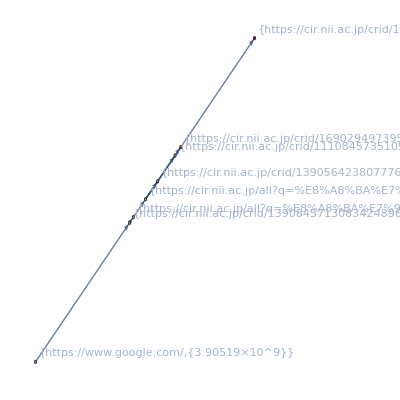
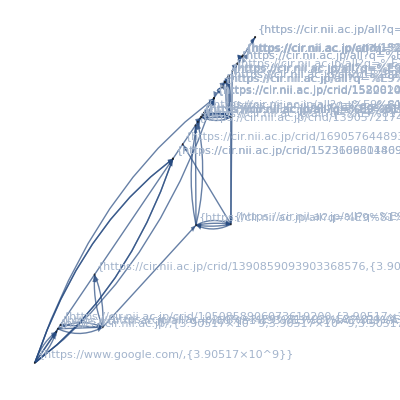
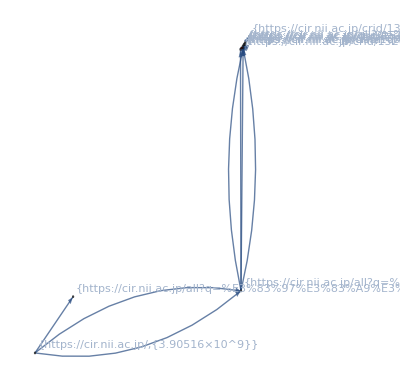
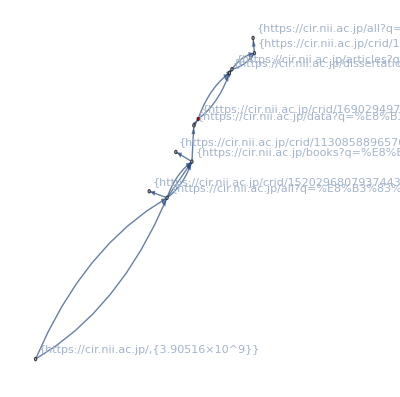
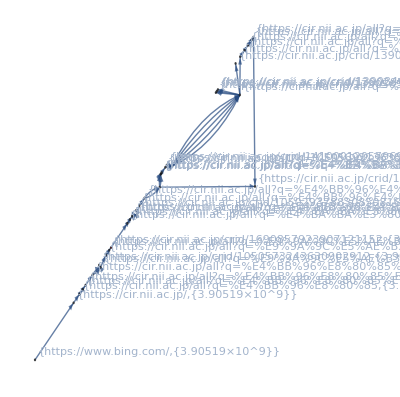
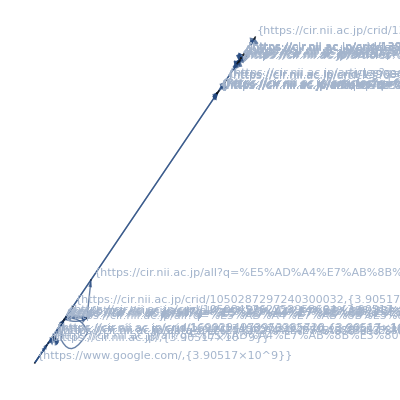
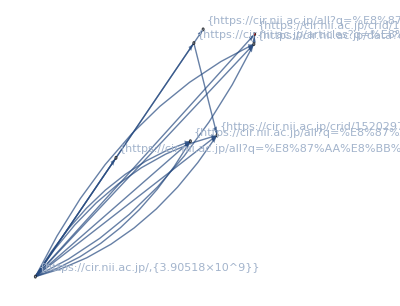
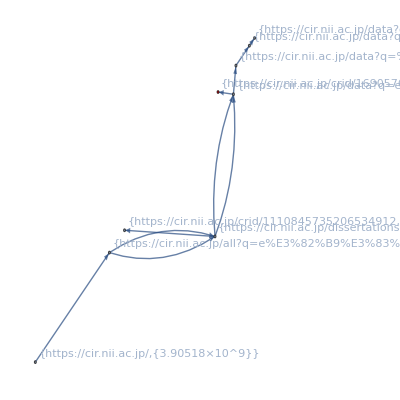

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 20179344
10365381

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 115
6
119 | 105
4
105

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 120993
20

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20 | 11972 | 1
14948 | 1
15506 | 1
18041 | 1
20660 | 1
23795 | 1
28039 | 1
35755 | 1
36536 | 1
43362 | 1
43362 | 1
46978 | 1
49038 | 1
52556 | 1
52556 | 1
59837 | 1
60099 | 1
64496 | 1
68256 | 1
90375 | 1 | 8
40
11
11
36
52
8
9
9
36
38
2
2
32
31
12
23
8
10
8 | 7
63
14
16
45
66
15
10
8
52
54
1
2
39
36
30
34
10
11
9 | 3.03333
23.1667
27.85
0.933333
8.96667
214.083
2.26667
4.43333
1.03333
0.783333
24.3
0
158.033
26.5667
27.1
0.833333
4.35
44.2667
13.1333
0.783333 | 4.41667
108.417
30.5667
3.01667
31.5
345.333
6.4
7.76667
2.31667
10.9833
35.35
0.
158.033
76.8667
76.75
5.56667
16.1
46.85
15.8167
2.66667

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{121}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{121}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.908018354141369×10^9

```mathematica
end-start
```

887.682079